#### Homework 2 - Nikola Totev | FN 62271 | Group 6

```mathematica
(*Exercise 1*)
```

```mathematica
nodes={1, 2,2.5, 3, 4, 5};
values= {0, 5, 6.5, 7, 3 ,1};
```

```mathematica
dividedDiff[nodes_,vals_]:=(If[Length[nodes]==1,vals[[1]],((dividedDiff[nodes[[2;;Length[nodes]]],vals[[2;;Length[nodes]]]]-dividedDiff[nodes[[1;;Length[nodes]-1]],vals[[1;;Length[nodes]-1]]])/(nodes[[Length[nodes]]]-nodes[[1]]))]);
newtonPoly[nodes_, values_, x_] := 
(values[[1]]+Sum[dividedDiff[nodes[[1;;n]], values[[1;;n]]]*Product[x-nodes[[i]],{i,1,n-1}], {n, 2, Length[nodes]}]);
```

```mathematica
polyPowOne[x_] = newtonPoly[{nodes[[4]], nodes[[5]]},{values[[4]], values[[5]]} , x];
polyPowTwo[x_] = newtonPoly[nodes[[3;;5]], values[[3;;5]], x];
polyPowThree[x_]  = newtonPoly[nodes[[2;;5]], values[[2;;5]], x];
polyMax[x_] = newtonPoly[nodes, values, x];

powOneResult = polyPowOne[3.4];
powTwoResult = polyPowTwo[3.4];
powThreeResult = polyPowThree[3.4];
powMaxResult = polyMax[3.4];
```

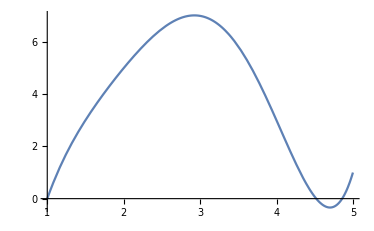
-Graphics-
5.4
6.2
6.344
6.21229

```mathematica
maxPolyPlot = Plot[polyMax[x], {x, 1, 5}];
Show[maxPolyPlot]

powOneResult
powTwoResult
powThreeResult
powMaxResult
```

```mathematica
(*Exercise 2*)
```

```mathematica
LagrangeBasics[k_, nodes_, x_]:= (
basePoly=1;
For[i = 1, i ≤  Length[nodes], i++,  If[i==k, basePoly*=1 , basePoly*=  (x-nodes[[i]])/(nodes[[k]]- nodes[[i]])]];
basePoly //Expand
);
```

```mathematica
Lagrange[nodes_, values_, x_] := (
finalPoly = 0;
For[j = 1, j≤ Length[nodes],j++, finalPoly+= values[[j]]*LagrangeBasics[ j,nodes, x]];
finalPoly //Expand
);
```

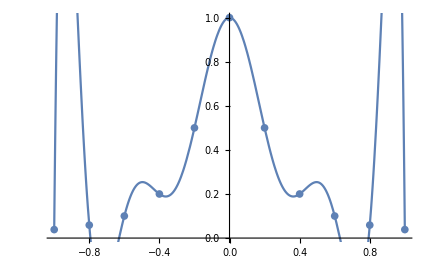
1.+2.2855×10^-16 x-16.8552 x^2-4.70457×10^-14 x^3+123.36 x^4-1.31339×10^-13 x^5-381.434 x^6+3.75033×10^-13 x^7+494.91 x^8-8.43769×10^-14 x^9-220.942 x^10
-Graphics-

```mathematica
(*Testing our creation*)
funcToInterpolate[x_]:= 1/(1+25*x^2);
funcNodes = {-1,-0.8,-0.6, -0.4, -0.2,0, 0.2 ,0.4,0.6, 0.8,1};
funcVal = funcToInterpolate[funcNodes];
lagrangeTest[x_] = Lagrange[funcNodes, funcVal, x];
lagrangeTest[x]
nodePlot = ListPlot[Transpose[{funcNodes,funcVal}]];
funcPlot = Plot[lagrangeTest[x], {x,-1, 1}];
Show[{nodePlot, funcPlot}]
```

```mathematica
(*Exercise 3*)
```

```mathematica
heightInMeters = Table[i*30000,{i,0,4}];
acceleration = {9.81,9.7487,9.6879,9.6278,9.5682};
```

```mathematica
accelerationPoly[x_] =Lagrange[heightInMeters, acceleration, x];
accelerationPoly[x]
```

```mathematica
accNodePolt = ListPlot[Transpose[{heightInMeters, acceleration}]];
accFuncPlot = Plot[accelerationPoly[x], {x, heightInMeters[[1]], heightInMeters[[Length[heightInMeters]]]}];
```

```mathematica
accelerationPoly[55000]//N
Show[{accNodePolt,accFuncPlot}]
```

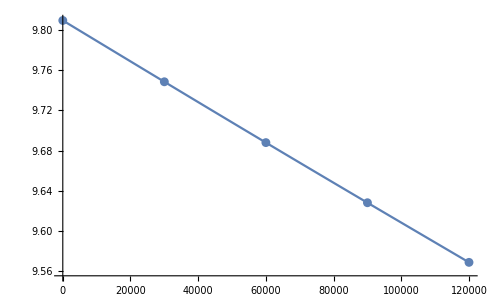
9.81-2.04611×10^-6 x-3.7037×10^-14 x^2+4.93827×10^-18 x^3-2.05761×10^-23 x^4
(*Acceleration at 55,000 meters*)
9.6979 
-Graphics-